Supporting information for A novel 3-d printed radial collimator for X-ray diffraction
Authors: S. Kowarik, L. Pithan, A. Zykov,  H. Wilming, L. Bogula, S. Boitano, P. Schäfer, H. Pithan, and F. Carla
For support contact linus.pithan@esrf.fr or stefan.kowarik@bam.de
Please cite our publication when using this code to generate your own radial collimator

## Transformation Functions and Constants

basis vectors

```mathematica
a1={Sin[Pi/3],Cos[Pi/3]};
a2={Sin[Pi/3],-Cos[Pi/3]};
```

scale factor

```mathematica
αfactor=0.0027779;
```

transformations

```mathematica
SphereToCartesian[{r_,theta_,phi_}]:={r Sin[theta] Cos[phi],r Sin[theta] Sin[phi],r Cos[theta]};
SphereToCartesian[r_,theta_,phi_]:=SphereToCartesian[{r,theta,phi}];
SphereToCartesian[r_,{theta_,phi_}]:=SphereToCartesian[{r,theta,phi}];
ScaledSphereToCartesian[{theta_,phi_},{α_,β_,unused_}]:= SphereToCartesian[{1,Pi*ArcTan[α theta ^β],phi}];
ScaledSphereToCartesian2[{theta_,phi_},{α_,β_,unused_},r_]:= SphereToCartesian[{1,Pi*ArcTan[r α theta ^β],phi}];(*messed-up*)
ToSpherical[{x_,y_,z_}]:={ArcCos[z/Sqrt[x^2+y^2+z^2]],ArcTan[x,y]};
```

rotation matrices

```mathematica
Ry=({{Cos[Pi/2], 0, Sin[Pi/2]}, {0, 1, 0}, {-Sin[Pi/2], 0, Cos[Pi/2]}});
rotwink=-15 (*war mal 15*)
Rx[phi_]:=({{Cos[-rotwink Degree], Sin[-rotwink Degree], 0}, {-Sin[-rotwink Degree], Cos[-rotwink Degree], 0}, {0, 0, 1}}).({{1, 0, 0}, {0, Cos[phi], Sin[phi]}, {0, -Sin[phi], Cos[phi]}});
```

-15

transfer functions from lattice points to theta,phi couples

```mathematica
(*NonLinScale[x_]:=5*(1-Exp[-.03*x])+1*)
(*.025*x+0.0023*x*x+1*)
NonLinScale[x_]:=Exp[0.045*x]+0.5*Erfc[(x-4)*.1]+2/(x+.1)
NonLinScale[3]
NonLinScale[6]
```

2.34593

2.02648

```mathematica
PointOnUnitSphere[i_,j_,a_]:=Ry.Rx[a⟦3⟧].If[i==0 && j==0,{0,0,1},ScaledSphereToCartesian2[ToPolarCoordinates[i*a1 + j*a2],a,NonLinScale[Norm[i a1+j a2]]]];
PointOnUnitSphere[{i_,j_},a_]:=PointOnUnitSphere[i,j,a];
```

```mathematica
NonLinScale[11]
```

1.98178

```mathematica
NonLinScale[6]
```

2.02648

```mathematica
27.3
```

27.3

## Geometrical Parameters of Collimator Structure (to be adopted for each use case)

```mathematica
detDis=550; (** Sample detector distance in mm**)
xdis1 = 20;  (** Distance from sample to front side on x axis in mm**)
xdis2 =750; (** Distance from sample to back side on x mm axis**)
```

```mathematica
detYsize=230;  (** Horizontal detector size in mm**)
detZsize=230;  (** Vertical detector size in mm**)
detYminus=-5; (** Offset to define direct beam position in y - direction **)
detZminus=-5; (** Offset to define direct beam position in z - direction **)
```

```mathematica
oAng=.3; (** Opening angle for one indivitual channel in degree **)
```

```mathematica
ijrange=30; (**max number of grid points in each directions ... must be chosen large enough to cover the whole collimator area; depends on detector size and cannel opening angle**)
```

parameters that should usually stay  the same for all calculations

```mathematica
margin=15oAng*Degree;(*!!!! adopt for width of soller channels !!!*)
R1=0.8*xdis1;(**defines the radius of the front side calculation; will be cropped later **)
R2=1.5*xdis2; (**defines the radius of the back side calculation; will be cropped later **)
```

```mathematica
outerStructurePath = NotebookDirectory[]<>"RadialCollimatorBox.scad"; (** Path to save dimensions of outer box for openSCAD **)
innerStructurePath = NotebookDirectory[]<>"RadialCollimatorGrid.scad";(** Path to save honeycomb structure for openSCAD **)
innerStructurePathPartial=NotebookDirectory[]<>"RadialCollimatorGridPart_";(**Path to save honeycomb structure for openSCAD**)PartLength=1000;
```

## Calculation of outside box

```mathematica
{θ1,ϕ1}=N[ToSpherical[{detDis,detYminus,detZminus}]]
{θ2,ϕ2}=N[ToSpherical[{detDis,detYminus,detZminus+detZsize}]]
{θ3,ϕ3}=N[ToSpherical[{detDis,detYminus+detYsize,detZminus+detZsize}]]
{θ4,ϕ4}=N[ToSpherical[{detDis,detYminus+detYsize,detZminus}]]
```

{1.57989,-0.00909066}

{1.18249,-0.00909066}

{1.20884,0.388319}

{1.57921,0.388319}

```mathematica
c1ThetaMinPhiMin=Round[SphereToCartesian[r,θ2,ϕ2]/.Flatten[NSolve[SphereToCartesian[r,θ2,ϕ2]⟦1⟧==xdis1,{r}]],.1]
c1ThetaMaxPhiMin=Round[SphereToCartesian[r,θ1,ϕ1]/.Flatten[NSolve[SphereToCartesian[r,θ1,ϕ1]⟦1⟧==xdis1,{r}]],.1]
c1ThetaMinPhiMax=Round[SphereToCartesian[r,θ3,ϕ3]/.Flatten[NSolve[SphereToCartesian[r,θ3,ϕ3]⟦1⟧==xdis1,{r}]],.1]
c1ThetaMaxPhiMax=Round[SphereToCartesian[r,θ4,ϕ4]/.Flatten[NSolve[SphereToCartesian[r,θ4,ϕ4]⟦1⟧==xdis1,{r}]],.1]
```

{20.,-0.2,8.2}

{20.,-0.2,-0.2}

{20.,8.2,8.2}

{20.,8.2,-0.2}

```mathematica
c2ThetaMinPhiMin=Round[SphereToCartesian[r,θ2,ϕ2]/.Flatten[NSolve[SphereToCartesian[r,θ2,ϕ2]⟦1⟧==xdis2,{r}]],.1]
c2ThetaMaxPhiMin=Round[SphereToCartesian[r,θ1,ϕ1]/.Flatten[NSolve[SphereToCartesian[r,θ1,ϕ1]⟦1⟧==xdis2,{r}]],.1]
c2ThetaMinPhiMax=Round[SphereToCartesian[r,θ3,ϕ3]/.Flatten[NSolve[SphereToCartesian[r,θ3,ϕ3]⟦1⟧==xdis2,{r}]],.1]
c2ThetaMaxPhiMax=Round[SphereToCartesian[r,θ4,ϕ4]/.Flatten[NSolve[SphereToCartesian[r,θ4,ϕ4]⟦1⟧==xdis2,{r}]],.1]
```

{750.,-6.8,306.8}

{750.,-6.8,-6.8}

{750.,306.8,306.8}

{750.,306.8,-6.8}

for further calculation:

```mathematica
thetaMin=Min[{θ1,θ2,θ3,θ4}]
thetaMax=Max[{θ1,θ2,θ3,θ4}]
phiMin=Min[{ϕ1,ϕ2,ϕ3,ϕ4}]
phiMax=Max[{ϕ1,ϕ2,ϕ3,ϕ4}]
```

1.18249

1.57989

-0.00909066

0.388319

calculate the faces / corners of the box :

```mathematica
fNormalArrow[face_,vector_]:=Arrow[{(face⟦3⟧-face⟦1⟧)/2+face⟦1⟧,(face⟦3⟧-face⟦1⟧)/2+face⟦1⟧+vector*xdis1/2}]  (**just for visualisation**);
```

```mathematica
faceFront={c1ThetaMinPhiMin,c1ThetaMaxPhiMin,c1ThetaMaxPhiMax,c1ThetaMinPhiMax};
faceBack={c2ThetaMinPhiMin,c2ThetaMaxPhiMin,c2ThetaMaxPhiMax,c2ThetaMinPhiMax};
fNormFront=Normalize[Cross[c1ThetaMaxPhiMax-c1ThetaMaxPhiMin,c1ThetaMinPhiMin-c1ThetaMaxPhiMax]];
fNormBack=-Normalize[Cross[c2ThetaMaxPhiMax-c2ThetaMaxPhiMin,c2ThetaMinPhiMin-c2ThetaMaxPhiMax]];
Graphics3D[{Polygon[faceFront],Polygon[faceBack],fNormalArrow[faceFront,fNormFront],fNormalArrow[faceBack,fNormBack]}]
```

-Graphics3D-

```mathematica
faceLeft={c1ThetaMinPhiMin,c2ThetaMinPhiMin,c2ThetaMaxPhiMin,c1ThetaMaxPhiMin};
faceRight={c1ThetaMinPhiMax,c2ThetaMinPhiMax,c2ThetaMaxPhiMax,c1ThetaMaxPhiMax};
fNormLeft=Normalize[Cross[c1ThetaMinPhiMin-c2ThetaMinPhiMin,c1ThetaMinPhiMin-c2ThetaMaxPhiMin]];
fNormRight=-Normalize[Cross[c1ThetaMinPhiMax-c2ThetaMinPhiMax,c1ThetaMinPhiMax-c2ThetaMaxPhiMax]];
Graphics3D[{Polygon[faceLeft],Polygon[faceRight],fNormalArrow[faceLeft,fNormLeft],fNormalArrow[faceRight,fNormRight]}]
```

-Graphics3D-

```mathematica
faceTop={c1ThetaMaxPhiMin,c2ThetaMaxPhiMin,c2ThetaMaxPhiMax,c1ThetaMaxPhiMax};
faceBottom={c1ThetaMinPhiMin,c2ThetaMinPhiMin,c2ThetaMinPhiMax,c1ThetaMinPhiMax};
fNormTop=Normalize[Cross[c1ThetaMaxPhiMin-c2ThetaMaxPhiMin,c1ThetaMaxPhiMin-c2ThetaMaxPhiMax]];
fNormBottom=-Normalize[Cross[c1ThetaMinPhiMin-c2ThetaMinPhiMin,c1ThetaMinPhiMin-c2ThetaMinPhiMax]];
Graphics3D[{Polygon[faceTop],Polygon[faceBottom],fNormalArrow[faceTop,fNormTop],fNormalArrow[faceBottom,fNormBottom]}]
```

-Graphics3D-

```mathematica
Graphics3D[{Polygon[faceTop],Polygon[faceBottom],Polygon[faceLeft],Polygon[faceRight],Polygon[faceFront],Polygon[faceBack]}]
```

-Graphics3D-

```mathematica
box={{faceTop,fNormTop},{faceBottom,fNormBottom},{faceLeft,fNormLeft},{faceRight,fNormRight},{faceFront,fNormFront},{faceBack,fNormBack}}
```

{{{{20.,-0.2,-0.2},{750.,-6.8,-6.8},{750.,306.8,-6.8},{20.,8.2,-0.2}},{0.00904073,0.,0.999959}},{{{20.,-0.2,8.2},{750.,-6.8,306.8},{750.,306.8,306.8},{20.,8.2,8.2}},{0.378593,0.,-0.925563}},{{{20.,-0.2,8.2},{750.,-6.8,306.8},{750.,-6.8,-6.8},{20.,-0.2,-0.2}},{0.00904073,0.999959,0.}},{{{20.,8.2,8.2},{750.,306.8,306.8},{750.,306.8,-6.8},{20.,8.2,-0.2}},{0.378593,-0.925563,0.}},{{{20.,-0.2,8.2},{20.,-0.2,-0.2},{20.,8.2,-0.2},{20.,8.2,8.2}},{1.,0.,0.}},{{{750.,-6.8,306.8},{750.,-6.8,-6.8},{750.,306.8,-6.8},{750.,306.8,306.8}},{-1.,0.,0.}}}

```mathematica
boxExport="mybox="<>StringReplace[ToString[box,FormatType->CForm],{"List("-> "[",")"->"]"}]<>";"
```

mybox=[[[[20.,-0.2,-0.2],[750.,-6.800000000000001,-6.800000000000001],[750.,306.8,-6.800000000000001],[20.,8.200000000000001,-0.2]],[0.009040726397077823,0.,0.9999591317980016]],[[[20.,-0.2,8.200000000000001],[750.,-6.800000000000001,306.8],[750.,306.8,306.8],[20.,8.200000000000001,8.200000000000001]],[0.37859334989563304,0.,-0.9255631126048631]],[[[20.,-0.2,8.200000000000001],[750.,-6.800000000000001,306.8],[750.,-6.800000000000001,-6.800000000000001],[20.,-0.2,-0.2]],[0.009040726397077821,0.9999591317980016,0.]],[[[20.,8.200000000000001,8.200000000000001],[750.,306.8,306.8],[750.,306.8,-6.800000000000001],[20.,8.200000000000001,-0.2]],[0.37859334989563304,-0.9255631126048633,0.]],[[[20.,-0.2,8.200000000000001],[20.,-0.2,-0.2],[20.,8.200000000000001,-0.2],[20.,8.200000000000001,8.200000000000001]],[1.,0.,0.]],[[[750.,-6.800000000000001,306.8],[750.,-6.800000000000001,-6.800000000000001],[750.,306.8,-6.800000000000001],[750.,306.8,306.8]],[-1.,0.,0.]]];

```mathematica
cornersExport="c1ThetaMinPhiMin="<>StringReplace[ToString[c1ThetaMinPhiMin,FormatType->CForm],{"List("-> "[",")"->"]"}]<>";\n"<>"c1ThetaMinPhiMax="<>StringReplace[ToString[c1ThetaMinPhiMax,FormatType->CForm],{"List("-> "[",")"->"]"}]<>";\n"<>"c1ThetaMaxPhiMin="<>StringReplace[ToString[c1ThetaMaxPhiMin,FormatType->CForm],{"List("-> "[",")"->"]"}]<>";\n"<>"c1ThetaMaxPhiMax="<>StringReplace[ToString[c1ThetaMaxPhiMax,FormatType->CForm],{"List("-> "[",")"->"]"}]<>";\n"<>"c2ThetaMinPhiMin="<>StringReplace[ToString[c2ThetaMinPhiMin,FormatType->CForm],{"List("-> "[",")"->"]"}]<>";\n"<>"c2ThetaMinPhiMax="<>StringReplace[ToString[c2ThetaMinPhiMax,FormatType->CForm],{"List("-> "[",")"->"]"}]<>";\n"<>"c2ThetaMaxPhiMin="<>StringReplace[ToString[c2ThetaMaxPhiMin,FormatType->CForm],{"List("-> "[",")"->"]"}]<>";\n"<>"c2ThetaMaxPhiMax="<>StringReplace[ToString[c2ThetaMaxPhiMax,FormatType->CForm],{"List("-> "[",")"->"]"}]<>";\n"
```

c1ThetaMinPhiMin=[20.,-0.2,8.200000000000001];
c1ThetaMinPhiMax=[20.,8.200000000000001,8.200000000000001];
c1ThetaMaxPhiMin=[20.,-0.2,-0.2];
c1ThetaMaxPhiMax=[20.,8.200000000000001,-0.2];
c2ThetaMinPhiMin=[750.,-6.800000000000001,306.8];
c2ThetaMinPhiMax=[750.,306.8,306.8];
c2ThetaMaxPhiMin=[750.,-6.800000000000001,-6.800000000000001];
c2ThetaMaxPhiMax=[750.,306.8,-6.800000000000001];

```mathematica
Export[outerStructurePath,boxExport<>"\n"<>cornersExport,"Text"]
```

/users/pithan/Documents/2018/soller_id31/20181011/erf_1ox_20_750_03_045__4_01_m15_quotation_2020/RadialCollimatorBox.scad

```mathematica
.
```

## Calculation of inner comb structure

```mathematica
α=oAng*αfactor;
params={α,1.00,0Degree}; (** 3rd parameter: rotation of grid around beam axis **)
```

```mathematica
thetaMinG=thetaMin-margin;
thetaMaxG=thetaMax+margin;
phiMinG=phiMin-margin;
phiMaxG=phiMax+margin;
```

Generating list of lattice points that represent the center of the combs

```mathematica
centerIndex=Flatten[Table[{k-l,k+2l},{k,-ijrange,ijrange},{l,-ijrange,ijrange}],1];
centers=Map[{#⟦1⟧,#⟦2⟧,ToSpherical[PointOnUnitSphere[#⟦1⟧,#⟦2⟧,params]]}&,centerIndex];
centersSpRed=Select[centers,#⟦3,1⟧>=thetaMinG&&#⟦3,1⟧<=thetaMaxG&&#⟦3,2⟧>=phiMinG&&#⟦3,2⟧≤phiMaxG&];
```

Generating list of lattice points that produce the honey-comb structure

```mathematica
latIndex=Join[Map[{(#⟦1⟧+1) , #⟦2⟧}&,centerIndex],Map[{#⟦1⟧ , (#⟦2⟧+1)}&,centersSpRed⟦All,1;;2⟧]];
```

```mathematica
latticeSpRed=Map[{#⟦1⟧,#⟦2⟧,ToSpherical[PointOnUnitSphere[#⟦1⟧,#⟦2⟧,params]]}&,latIndex];
```

Visualisation of collimator bounding box and all calculated lattice points

```mathematica
Show[{Graphics3D[{Red,Point[#]&/@Map[PointOnUnitSphere[#,params]&,centerIndex],Green,Point[{1,0,0}]}],Graphics3D[Sphere[{0,0,0},1]],Graphics3D[{Polygon[{SphereToCartesian[0,thetaMinG,phiMinG],SphereToCartesian[1.1,thetaMinG,phiMinG],SphereToCartesian[1.1,thetaMaxG,phiMinG],SphereToCartesian[0,thetaMaxG,phiMinG]}],Polygon[{SphereToCartesian[0,thetaMinG,phiMaxG],SphereToCartesian[1.1,thetaMinG,phiMaxG],SphereToCartesian[1.1,thetaMaxG,phiMaxG],SphereToCartesian[0,thetaMaxG,phiMaxG]}],
Polygon[{SphereToCartesian[0,thetaMinG,phiMinG],SphereToCartesian[1.1,thetaMinG,phiMinG],SphereToCartesian[1.1,thetaMinG,phiMaxG],SphereToCartesian[0,thetaMinG,phiMaxG]}],Polygon[{SphereToCartesian[0,thetaMaxG,phiMinG],SphereToCartesian[1.1,thetaMaxG,phiMinG],SphereToCartesian[1.1,thetaMaxG,phiMaxG],SphereToCartesian[0,thetaMaxG,phiMaxG]}]}]}]
```

-Graphics3D-

Visualisation of collimator box and lattice points selected to generate the collimator walls

```mathematica
Show[{Graphics3D[{Red,Point[#]&/@Map[PointOnUnitSphere[#,params]&,centersSpRed⟦All,1;;2⟧],Green,Point[{0,0,1}]}],Graphics3D[Sphere[{0,0,0},1]],Graphics3D[{Polygon[{SphereToCartesian[0,thetaMinG,phiMinG],SphereToCartesian[1.1,thetaMinG,phiMinG],SphereToCartesian[1.1,thetaMaxG,phiMinG],SphereToCartesian[0,thetaMaxG,phiMinG]}],Polygon[{SphereToCartesian[0,thetaMinG,phiMaxG],SphereToCartesian[1.1,thetaMinG,phiMaxG],SphereToCartesian[1.1,thetaMaxG,phiMaxG],SphereToCartesian[0,thetaMaxG,phiMaxG]}],
Polygon[{SphereToCartesian[0,thetaMinG,phiMinG],SphereToCartesian[1.1,thetaMinG,phiMinG],SphereToCartesian[1.1,thetaMinG,phiMaxG],SphereToCartesian[0,thetaMinG,phiMaxG]}],Polygon[{SphereToCartesian[0,thetaMaxG,phiMinG],SphereToCartesian[1.1,thetaMaxG,phiMinG],SphereToCartesian[1.1,thetaMaxG,phiMaxG],SphereToCartesian[0,thetaMaxG,phiMaxG]}]}]}]
```

-Graphics3D-

#### Generation of walls for honey comb structure

```mathematica
Clear[latticepointSp]
Scan[(latticepointSp[#⟦1⟧,#⟦2⟧]=#⟦3⟧)&,latticeSpRed];
latticepointSp[_,_]=Infinity;
```

```mathematica
getWall[ceni_,cenj_,r1_,r2_]:=Module[{a,b,c,d,tmp},
a= latticepointSp[ceni-1,cenj];
b=latticepointSp[ceni,cenj-1];
c=latticepointSp[ceni+1,cenj-1];
d=latticepointSp[ceni+1,cenj];
tmp={};
If[Max[a]≠Infinity&&Max[b]≠Infinity,tmp=AppendTo[tmp,{SphereToCartesian[r1,a⟦1⟧,a⟦2⟧],SphereToCartesian[r2,a⟦1⟧,a⟦2⟧],SphereToCartesian[r2,b⟦1⟧,b⟦2⟧],SphereToCartesian[r1,b⟦1⟧,b⟦2⟧]}]];
If[Max[b]≠Infinity&&Max[c]≠Infinity,tmp=AppendTo[tmp,{SphereToCartesian[r1,b⟦1⟧,b⟦2⟧],SphereToCartesian[r2,b⟦1⟧,b⟦2⟧],SphereToCartesian[r2,c⟦1⟧,c⟦2⟧],SphereToCartesian[r1,c⟦1⟧,c⟦2⟧]}]];
If[Max[c]≠Infinity&&Max[d]≠Infinity,tmp=AppendTo[tmp,{SphereToCartesian[r1,c⟦1⟧,c⟦2⟧],SphereToCartesian[r2,c⟦1⟧,c⟦2⟧],SphereToCartesian[r2,d⟦1⟧,d⟦2⟧],SphereToCartesian[r1,d⟦1⟧,d⟦2⟧]}]];
tmp
]
```

```mathematica
myWalls=Flatten[getWall[#⟦1⟧,#⟦2⟧,R1,R2]&/@centersSpRed,1];
```

```mathematica
wallExport="mywalls="<>StringReplace[ToString[myWalls,FormatType->CForm],{"List("-> "[",")"->"]"}]<>";";
```

```mathematica
Export[innerStructurePath,wallExport,"Text"]
```

/users/pithan/Documents/2018/soller_id31/20181011/erf_1ox_20_750_03_045__4_01_m15_quotation_2020/RadialCollimatorGrid.scad

## Visualisation of collimator (not yet cropped to it's bounding box)

```mathematica
Graphics3D[{Polygon[#]&/@myWalls,Red,Polygon[{SphereToCartesian[R1,thetaMin,phiMin],SphereToCartesian[R2,thetaMin,phiMin],SphereToCartesian[R2,thetaMax,phiMin],SphereToCartesian[R1,thetaMax,phiMin]}],Polygon[{SphereToCartesian[R1,thetaMin,phiMax],SphereToCartesian[R2,thetaMin,phiMax],SphereToCartesian[R2,thetaMax,phiMax],SphereToCartesian[R1,thetaMax,phiMax]}],
Polygon[{SphereToCartesian[R1,thetaMin,phiMin],SphereToCartesian[R2,thetaMin,phiMin],SphereToCartesian[R2,thetaMin,phiMax],SphereToCartesian[R1,thetaMin,phiMax]}],Polygon[{SphereToCartesian[R1,thetaMax,phiMin],SphereToCartesian[R2,thetaMax,phiMin],SphereToCartesian[R2,thetaMax,phiMax],SphereToCartesian[R1,thetaMax,phiMax]}]}]
```

-Graphics3D-

Once this Notebook has run through, please use open the file "GenerateRadialCollimator.scad" in OpenSCAD ( http://www.openscad.org/ ) with the two files generated by this notebook saved in the same folder as “GenerateRadialCollimator.scad” to calculate the 3d printable stl file

### Calculating opening angle and individual comb dimensions for diagnostics

calculating the opening angle for all channels

```mathematica
OpenAng[p1_,p2_]:=ArcCos[p1.p2]/Degree;
```

```mathematica
calcAng[{i_,j_},a_]:={OpenAng[PointOnUnitSphere[i,j-1,a],PointOnUnitSphere[i,j+1,a]],OpenAng[PointOnUnitSphere[i-1,j,a],PointOnUnitSphere[i+1,j,a]],OpenAng[PointOnUnitSphere[i+1,j-1,a],PointOnUnitSphere[i-1,j+1,a]]}
```

```mathematica
oa=Map[{#⟦1⟧,#⟦2⟧,calcAng[{#⟦1⟧,#⟦2⟧},params]}&,centersSpRed];
```

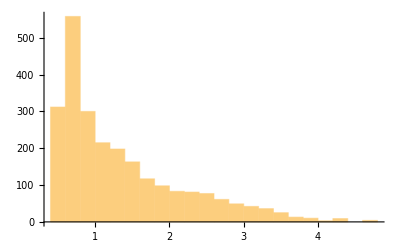

```mathematica
Histogram[Flatten[oa[[All,3]]]]  (**Opening angle in degree of all channels**)
```

```mathematica
(**opening angles calculated along the three diagonals in each comb seperatly**)
```

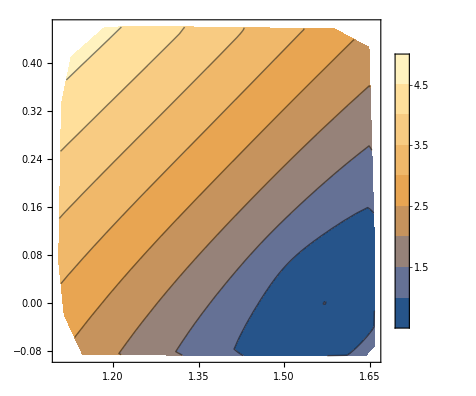

```mathematica
ListContourPlot[Map[Flatten[{ToSpherical[PointOnUnitSphere[#⟦1⟧,#⟦2⟧,params]],#⟦3,1⟧}]&,oa],PlotLegends->Automatic,AspectRatio->Automatic]
```

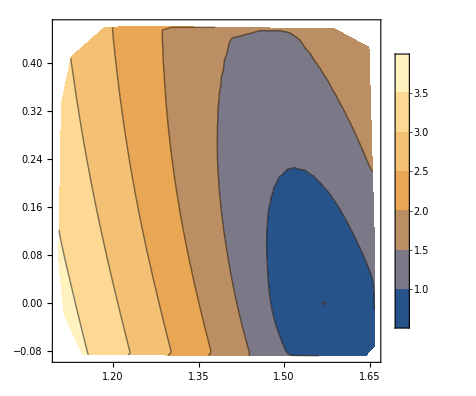

```mathematica
ListContourPlot[Map[Flatten[{ToSpherical[PointOnUnitSphere[#⟦1⟧,#⟦2⟧,params]],#⟦3,2⟧}]&,oa],PlotLegends->Automatic,AspectRatio->Automatic]
```

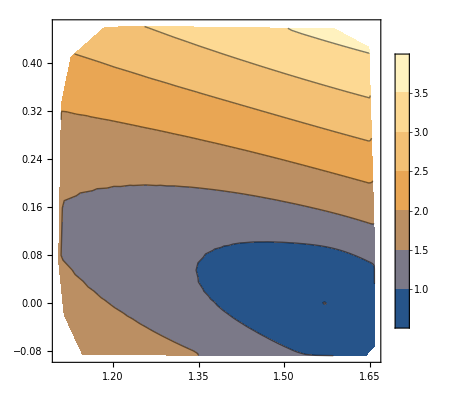

```mathematica
ListContourPlot[Map[Flatten[{ToSpherical[PointOnUnitSphere[#⟦1⟧,#⟦2⟧,params]],#⟦3,3⟧}]&,oa],PlotLegends->Automatic,AspectRatio->Automatic]
```

Diameter of combs at front and back side of the collimator

```mathematica
meanOA=Mean[Flatten[oa[[All,3]]]]*Degree;
```

```mathematica
2*xdis1*Tan[meanOA/2] (**comb diameter at the front side in mm**)
```

0.469206

```mathematica
2*xdis2*Tan[meanOA/2] (**comb diameter at the detector side in mm**)
```

17.5952

### Save Partial files

```mathematica
a=myWalls;
n=1;
While[Length[a]>PartLength,{b,a}=TakeDrop[a,PartLength];
wallExportPart="mywalls="<>StringReplace[ToString[b,FormatType->CForm],{"List("->"[",")"->"]"}]<>";";
Export[innerStructurePathPartial<>IntegerString[n,10,3]<>".scad",wallExportPart,"Text"];
n=n+1]
If[Length[a]>0,wallExportPart="mywalls="<>StringReplace[ToString[a,FormatType->CForm],{"List("->"[",")"->"]"}]<>";";
Export[innerStructurePathPartial<>IntegerString[n,10,3]<>".scad",wallExportPart,"Text"];]
```

```mathematica
Max[Map[N[Norm[#[[1]]a1+#[[2]]a2]]&,centersSpRed]]
```

39.1535